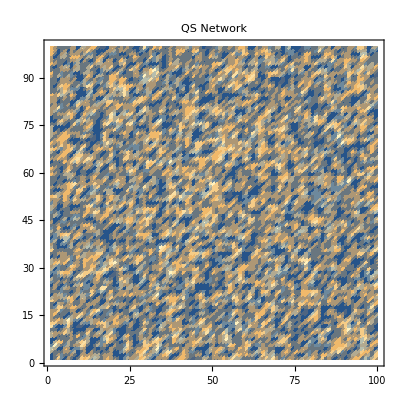

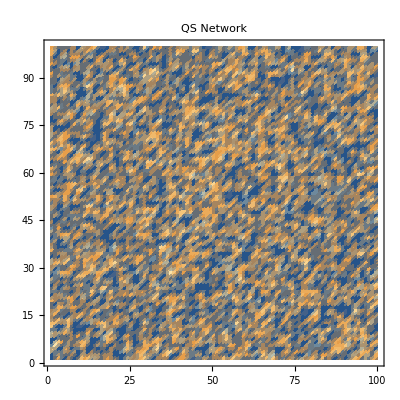

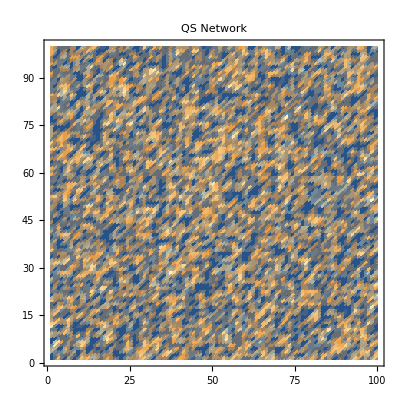

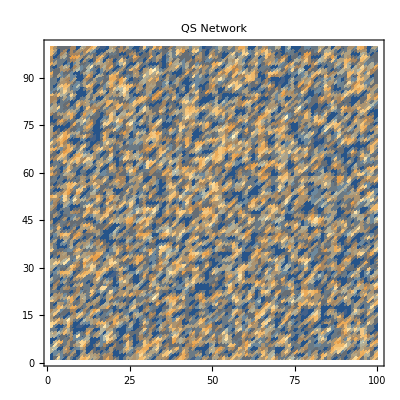

Set::take: Cannot take positions 1 through 30 in {72}.

Part::partw: Part 2 of {{89,71}} does not exist.

Part::partw: Part 3 of {{89,71}} does not exist.

Part::partw: Part 4 of {{89,71}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::take: Cannot take positions 1 through 30 in {}.

Set::take: Cannot take positions 1 through 30 in {76,92,123,108,128,84,105,98,94,134,63,97,105,120,104,108,75,74,97}.

General::stop: Further output of Set::take will be suppressed during this calculation.

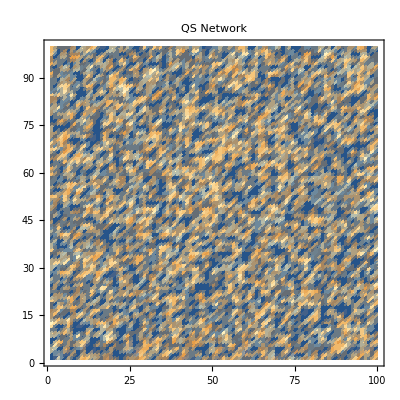

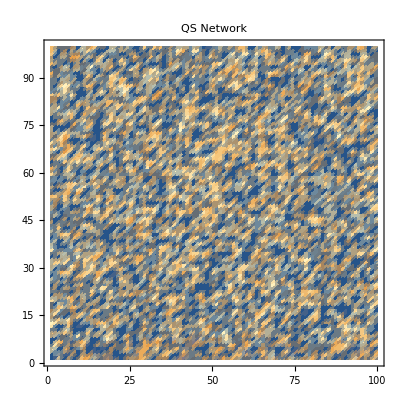

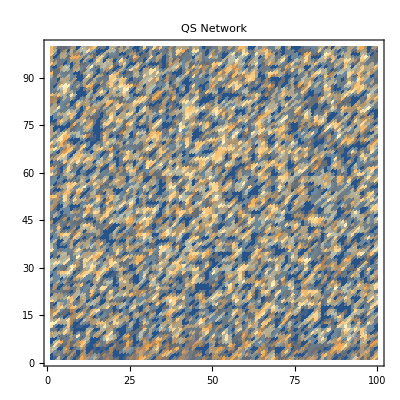

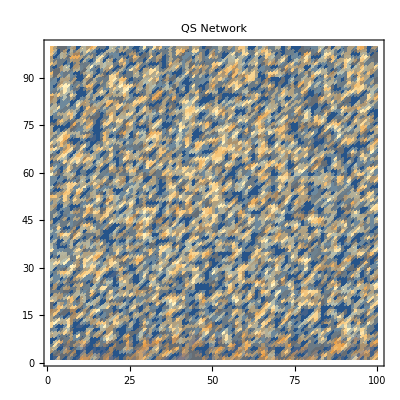

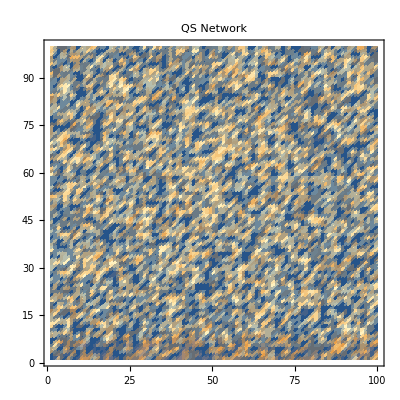

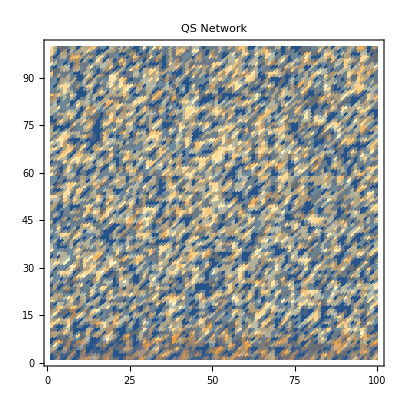

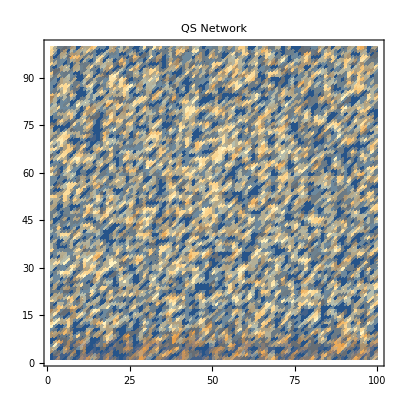

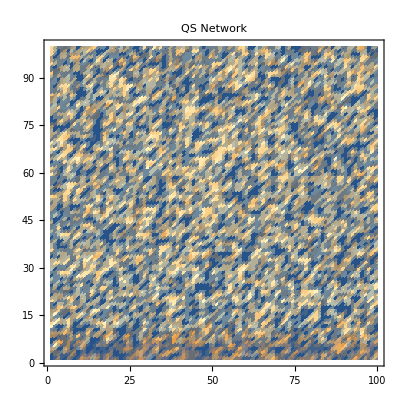

-Graphics-

-Graphics-

-Graphics-

```mathematica
areaSize=100;
cellDensity=0.5;
observationTime=20;
timeforSignaling=1;

cellDistribution[]:=HalfNormalDistribution[0.5];

(*Auxiliary signalling functions*)
neigh={};
For[k=1,k≤15,k++,
neighborhood=Table[Max[0,k-Abs[x]-Abs[y]],{x,-5,5},{y,-5,5}];
neigh=Append[neigh,neighborhood]]; 

aiDomain={1,2,3,4,5,6,7,8,9,10};

aiConcentration[level_]:=Switch[level,1,neigh[[3]],2,neigh[[5]],3,neigh[[7]],4,neigh[[9]],5,neigh[[8]],6,neigh[[7]],7,neigh[[6]],8,neigh[[5]],9,neigh[[4]],10,neigh[[3]]];

aiCell[level_]:=Switch[level,1,1,2,3,3,5,4,7,5,6,6,5,7,4,8,3,9,2,10,1];

aiDistance[level_]:=1+aiCell[level];

aiUpdate[levels_,lccore_]:=(levelsNew=levels;
cellPos1=Position[levels[[First[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
If[x==1, conc1[[1;;30]]=0;
ps1 ={cellPos1[[1]],cellPos1[[2]],cellPos1[[3]],cellPos1[[4]],cellPos1[[5]]};
];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]>First[aiDomain]+3,levelsNew[[First[aiDomain]+1]]=ReplacePart[levelsNew[[First[aiDomain]+1]],1,cellPos1[[s]]];levelsNew[[First[aiDomain]]]=ReplacePart[levelsNew[[First[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
cellPos1=Position[levels[[Last[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
If[x==1, conc1[[1;;30]]=0;
ps2 ={cellPos1[[1]],cellPos1[[2]],cellPos1[[3]],cellPos1[[4]],cellPos1[[5]]};
ps1 = Append[ps1,ps2];
Clear[ps2];
];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]<Last[aiDomain]+3,levelsNew[[Last[aiDomain]-1]]=ReplacePart[levelsNew[[Last[aiDomain]-1]],1,cellPos1[[s]]];
levelsNew[[Last[aiDomain]]]=ReplacePart[levelsNew[[Last[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
For[r=First[aiDomain]+1,r<Last[aiDomain],r++,
cellPos1=Position[levels[[r]],1];
conc1=Extract[lccore,cellPos1];
If[x==1, conc1[[1;;30]]=0;
ps2 ={cellPos1[[1]],cellPos1[[2]],cellPos1[[3]],cellPos1[[4]],cellPos1[[5]]};
ps1 = Append[ps1,ps2];
Clear[ps2];
];
For[s=1,s≤Length[conc1],s++,
If[conc1[[s]]<r+3,levelsNew[[r-1]]=ReplacePart[levelsNew[[r-1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]],If[conc1[[s]]>r+3,levelsNew[[r+1]]=ReplacePart[levelsNew[[r+1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]]];];];
];

levelsNew
);

(*Initializing all necessary data structures*)
levels=Table[0,{Last[aiDomain]-First[aiDomain]+1},{areaSize},{areaSize}];
levelsDynamic=levels;
levelsDynamicNew=levels;
levelsStatic=levels;
graph=Range[observationTime];
productionList=Range[observationTime];
cells=Table[If[Random[]<cellDensity,1,0],{i,areaSize},{j,areaSize}];

levels=ReplacePart[levels,cells,1];
lc=ListCorrelate[aiConcentration[1],cells,{-1,1},0];
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
levels=aiUpdate[levels,lccore];

nCells=Count[cells,1,2];
cellPos=Position[cells,1];
EdgeMatrix=Table[0,{nCells},{nCells}];

(*Main QS cycle*)
For[clock=1,clock≤observationTime,clock++,
(*update level and concentration table*)
If[Mod[clock,timeforSignaling]==0,
lc=Plus@@Function[{i},ListCorrelate[aiConcentration[i],levels[[i]],{-1,1},0]]/@aiDomain;
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
signalingCells=cells; 
For[k=1,k≤nCells,k++,
(*To avoid artificial cyclic activation-inhibition dependencies, only a small fraction of cells is signalling at once*)
If[Random[]<.8,signalingCells=ReplacePart[signalingCells,0,cellPos[[k]]]];
];
For[k=First[aiDomain],k≤Last[aiDomain],k++,
levelsStatic[[k]]=levels[[k]]-signalingCells;
mins=Position[levelsStatic[[k]],-1];
For[v=1,v≤Length[mins],v++,levelsStatic[[k]]=ReplacePart[levelsStatic[[k]],0,mins[[v]]]];
];
levelsDynamic=levels-levelsStatic;
(*To update make the signal disappear at 4s*)
If[ clock > 4 && clock<16, x=1;
];
levelsDynamicNew=aiUpdate[levelsDynamic,lccore];
levels=levelsDynamicNew+levelsStatic;
];
x=0;
graph[[clock]]=Plus@@Function[{i},aiDistance[i]*levels[[i]]]/@aiDomain;
Print[ListDensityPlot[graph[[clock]],PlotLabel->"QS Network"]];
productionList[[clock]]=N[Total[graph[[clock]],2]/nCells](*average ai production per cell*)
]; (*end main QS cycle*)
```

```mathematica
productionList
```

{4.40643,4.79897,5.1538,5.48998,5.73904,5.96527,6.13177,6.26791,6.36098,6.41476,6.46477,6.47589,6.45981,6.41338,6.3717,6.33717,6.28002,6.18277,6.08593,5.96984}

```mathematica
lc
```

{{0,0,0,0,0,0,0,1,2,3,4,3,2,1,0,0,0,1,2,3,2,1,0,0,0,0,0,0,0,0,0,1,2,1,0,0,0,0,0,0,0,1,2,1,0,0,0,1,2,1,0,0,0,0,0,0,0,2,4,4,2,1,0,1,3,5,5,4,4,2,1,3,5,6,5,3,2,4,5,4,4,3,2,2,3,3,1,0,0,0,0,0,1,2,2,2,2,4,5,4,5,5,5,5,3,2,1,0,0,0},{0,0,0,0,0,0,1,2,3,4,5,4,3,3,5,3,4,5,6,5,3,2,2,1,1,0,0,0,0,0,1,4,5,4,2,2,1,2,2,1,1,2,3,3,4,4,5,5,5,3,1,0,1,1,2,4,6,8,8,9,8,5,5,5,7,8,8,7,6,5,8,9,12,13,11,9,8,8,8,8,6,5,6,9,10,8,7,6,4,4,3,2,3,4,4,5,7,10,9,8,9,9,11,12,10,6,3,1,0,0},{0,0,0,0,1,3,5,8,8,7,7,5,5,7,9,10,11,10,9,9,5,5,6,5,3,1,0,0,0,1,5,8,11,10,6,4,5,7,5,5,5,4,5,6,10,12,9,8,7,5,3,2,4,3,4,8,12,15,15,12,11,12,14,14,13,14,14,12,11,12,17,19,21,20,18,17,15,14,13,12,11,10,12,14,15,15,12,12,12,9,7,6,7,8,10,15,18,20,19,17,15,16,18,20,18,13,8,4,1,0},{0,0,0,1,2,5,8,14,14,13,12,9,9,11,17,22,20,18,15,14,11,12,13,13,8,4,1,0,1,5,11,15,18,18,12,12,11,13,13,11,10,8,9,13,19,23,20,16,14,10,9,9,9,9,11,16,22,27,26,22,21,25,26,24,23,22,20,20,25,30,33,34,34,31,27,28,26,25,22,20,20,21,21,21,23,24,19,23,22,20,19,16,18,19,20,24,28,29,31,30,29,28,27,26,24,18,12,8,4,0},{0,0,1,2,3,9,15,20,20,19,18,17,16,20,32,37,33,29,25,23,21,23,23,22,16,10,7,6,10,16,22,27,30,26,27,25,24,26,24,22,19,16,19,27,31,35,34,29,24,19,20,19,17,17,22,29,35,40,39,39,42,41,41,37,36,32,29,32,43,50,54,51,49,45,41,41,40,36,34,32,33,34,35,34,35,36,36,39,37,34,34,33,35,38,37,38,41,43,46,48,48,43,39,35,31,24,16,12,8,1},{0,0,2,4,8,20,28,31,29,28,29,27,29,33,45,52,47,44,40,40,38,39,37,34,27,19,15,19,26,29,34,40,45,50,47,46,42,43,37,37,36,37,37,43,48,50,48,42,37,35,35,32,29,32,38,48,50,52,56,61,66,67,63,58,53,47,44,50,65,77,81,79,75,73,66,65,59,56,49,48,49,52,55,55,53,55,51,54,54,55,54,52,58,58,57,60,59,61,69,70,70,64,57,49,41,31,21,16,12,3},{0,0,4,8,15,27,39,46,45,44,47,44,44,46,57,65,61,56,54,51,48,49,49,41,31,23,22,28,37,44,46,51,60,69,66,60,57,55,50,47,49,52,57,62,64,65,61,56,53,51,50,45,41,43,50,59,61,66,70,76,80,78,76,70,66,62,58,65,83,94,96,91,88,80,72,70,68,61,53,48,54,56,60,62,62,67,64,68,71,74,74,74,78,73,69,73,73,75,81,87,86,82,78,65,54,40,26,19,14,5},{0,1,7,11,20,34,46,55,55,53,55,55,55,56,64,69,66,59,54,53,50,52,54,48,39,29,26,33,44,49,53,60,73,80,76,72,68,69,63,60,63,63,67,71,74,76,72,66,65,59,57,49,49,51,56,62,69,76,79,80,82,83,85,79,80,79,72,79,92,100,103,100,94,84,77,77,72,66,58,56,58,62,66,67,71,73,72,81,84,90,93,96,99,92,84,85,85,89,91,98,100,95,87,73,59,42,29,20,13,5},{0,3,9,15,28,41,56,65,66,65,65,63,64,63,68,71,72,65,62,62,59,58,57,55,51,44,39,44,55,59,63,71,81,85,84,81,77,76,74,71,78,76,79,83,85,87,83,80,79,73,67,60,64,65,63,73,84,92,94,92,89,86,87,84,89,90,84,88,94,102,108,105,99,90,87,87,80,77,67,65,66,66,71,74,79,82,79,88,94,99,105,108,112,105,99,99,98,103,104,108,110,104,93,80,66,45,31,20,12,4},{0,3,8,18,31,46,63,73,76,77,75,75,70,71,75,78,79,73,71,68,60,62,65,63,65,60,54,54,60,63,69,75,84,92,92,91,87,85,82,82,84,82,85,90,95,95,92,91,92,83,77,72,79,78,74,79,91,99,102,99,91,91,94,92,97,100,95,92,98,108,112,107,101,96,89,86,84,80,71,67,67,66,71,76,85,90,93,103,109,113,115,119,126,120,118,116,111,111,109,115,114,105,94,81,67,46,30,18,10,4},{0,4,10,21,39,56,72,81,85,87,91,88,82,82,85,87,87,81,80,76,72,75,78,81,77,69,66,67,68,69,72,78,89,100,102,104,101,100,98,97,96,91,99,106,111,114,109,105,101,99,95,93,98,98,94,96,101,107,106,101,94,94,97,96,102,104,100,99,108,117,117,116,116,105,99,96,93,92,85,75,69,68,78,85,92,98,104,113,117,120,124,128,136,134,133,135,128,123,119,129,127,116,104,88,73,50,30,18,11,4},{0,5,11,25,43,64,83,88,91,96,99,98,87,92,94,93,89,86,86,87,90,97,99,101,97,86,79,79,79,77,76,81,93,103,104,109,110,112,110,110,110,111,118,124,127,129,123,120,121,119,119,120,121,123,119,113,115,113,110,105,100,101,100,101,103,103,104,112,118,125,126,124,121,110,101,99,96,97,88,79,74,75,88,97,101,105,112,121,121,123,131,133,145,142,143,145,138,134,129,131,131,120,106,85,71,48,29,19,13,4},{1,7,16,29,51,73,94,101,108,109,106,102,95,97,101,97,96,97,101,103,113,122,123,122,118,107,95,96,94,90,86,88,97,107,107,112,116,121,121,119,123,128,135,142,137,137,129,128,129,132,136,138,136,135,126,122,118,118,116,116,107,103,104,105,105,108,116,124,133,138,139,134,128,117,108,102,106,105,96,89,83,85,100,108,113,113,119,125,127,129,133,138,148,149,154,155,151,151,147,147,144,133,118,93,71,45,31,19,11,4},{3,12,22,37,59,83,102,115,127,126,118,114,102,106,108,107,109,113,118,123,133,138,137,138,132,120,111,106,106,98,92,89,99,112,110,114,115,120,121,121,130,138,146,151,149,144,139,143,143,147,154,151,150,146,136,133,132,127,124,124,117,109,109,112,115,125,130,142,150,159,156,147,140,127,114,113,113,109,100,98,95,96,110,117,124,124,127,126,128,132,133,141,153,152,159,161,159,158,157,157,149,136,122,95,70,43,29,18,11,4},{6,14,25,40,64,91,113,125,132,130,127,119,113,115,115,112,112,115,122,135,148,151,152,151,144,134,123,112,113,109,100,100,109,119,119,120,120,122,125,131,141,150,155,158,157,148,147,148,149,155,158,160,157,155,147,140,133,130,124,122,118,113,112,118,126,134,139,151,156,161,156,150,145,129,121,117,113,105,100,100,100,104,116,123,135,139,137,131,132,136,139,146,155,158,166,168,166,165,161,161,151,136,121,97,71,43,25,16,8,2},{9,17,28,45,67,100,122,130,133,136,135,123,117,116,117,118,119,123,130,143,155,162,166,164,162,152,137,119,119,115,106,107,116,127,126,123,121,126,135,140,154,163,164,165,159,149,147,146,152,155,165,168,165,160,156,146,135,129,126,121,123,124,131,133,137,143,150,163,162,166,161,154,151,135,128,120,120,118,117,118,115,116,122,123,135,141,138,131,130,134,141,147,149,158,169,174,171,176,173,166,157,139,122,100,72,45,27,15,5,0},{10,20,35,51,74,107,131,141,144,147,148,136,126,121,126,127,132,138,141,155,166,173,178,178,174,163,149,130,128,130,121,119,119,127,126,125,121,124,137,142,152,163,168,170,158,146,145,145,151,156,161,166,165,162,153,144,134,129,125,121,123,128,140,140,143,152,163,174,171,173,167,158,156,141,132,129,130,129,128,128,128,125,122,122,133,140,139,134,134,132,139,143,144,157,167,168,173,179,175,167,153,136,119,99,69,46,31,14,3,0},{11,23,38,58,78,111,134,148,154,154,156,148,136,132,133,134,142,147,150,161,174,180,184,185,176,170,158,138,139,139,135,130,128,130,129,130,127,129,138,146,155,163,167,164,153,141,136,137,149,153,161,166,164,160,151,144,134,131,128,122,125,128,139,143,149,160,169,177,173,175,175,172,169,152,143,139,138,136,137,134,139,136,129,132,138,141,140,134,130,128,131,131,137,156,161,160,164,172,171,163,152,136,121,98,68,47,32,16,5,0},{11,22,40,59,79,111,136,154,164,164,164,152,148,136,137,141,147,151,156,164,173,173,180,181,177,174,166,151,151,146,141,135,133,134,128,131,127,126,135,140,153,163,165,164,152,138,133,132,141,145,156,162,160,156,147,144,132,132,131,127,129,129,141,146,153,163,171,182,177,180,183,180,178,159,151,147,144,141,141,141,146,146,140,141,147,145,140,133,129,125,126,125,130,146,154,155,158,166,166,157,148,138,123,99,70,49,33,17,6,1},{9,22,38,57,79,111,133,155,164,167,166,158,151,143,146,148,150,152,152,158,161,163,169,173,173,167,163,152,150,142,143,143,139,136,134,133,134,131,135,143,153,166,164,163,152,141,127,123,126,131,145,156,159,156,145,141,131,131,131,126,127,130,144,147,152,166,168,177,178,181,180,180,178,163,152,148,147,147,146,147,148,149,144,146,147,143,138,130,126,123,119,118,126,139,146,147,150,152,152,148,144,139,125,102,76,55,38,20,7,2},{9,20,36,57,83,112,134,156,164,169,173,166,159,151,153,153,154,154,152,155,160,163,173,175,173,166,162,153,149,141,141,138,137,133,130,130,133,131,136,145,160,172,170,164,156,142,131,120,119,123,138,147,152,151,145,145,136,132,129,128,135,135,146,145,152,167,169,175,175,177,176,177,175,163,158,159,153,156,159,152,153,159,158,156,151,147,139,130,123,117,114,114,124,135,139,139,139,142,143,144,146,144,134,109,85,61,40,20,6,1},{9,16,32,54,80,109,134,158,166,167,169,165,164,160,159,163,161,160,155,153,150,153,163,165,162,163,162,153,144,139,139,135,136,130,129,126,127,130,136,151,161,172,173,168,157,143,128,122,115,122,136,145,146,144,141,142,137,136,133,133,138,141,143,141,148,161,161,164,167,175,179,172,167,164,160,165,160,159,165,162,161,165,163,160,152,151,142,132,123,118,117,116,121,128,130,128,123,131,135,139,142,143,135,112,87,64,41,22,5,1},{9,14,28,49,74,102,130,152,160,163,165,163,165,162,162,161,162,163,157,151,146,152,155,159,158,159,161,157,148,142,139,135,133,135,132,130,127,133,141,152,162,170,173,167,157,144,134,125,117,120,134,139,144,141,142,146,142,141,137,137,143,145,145,134,137,150,152,151,156,166,171,165,159,159,159,164,160,162,170,167,168,171,173,171,162,160,149,139,132,127,126,122,119,128,129,129,123,130,135,140,140,142,138,120,93,65,44,25,9,2},{9,15,27,44,65,91,118,138,148,156,163,161,164,159,161,158,154,153,150,148,149,151,152,154,152,148,153,151,146,143,140,133,136,139,137,135,135,145,149,154,167,173,173,163,151,143,137,128,119,121,130,135,139,141,144,147,147,147,144,144,150,151,150,141,133,140,145,147,150,153,160,160,158,161,154,157,157,162,173,173,176,180,182,179,171,169,154,145,136,135,135,135,133,133,135,131,126,134,141,147,150,148,142,124,99,68,46,28,13,4},{7,15,27,40,62,87,110,130,140,148,160,160,162,161,164,156,143,138,142,149,150,147,150,150,146,143,146,148,143,140,140,136,138,140,138,145,150,156,156,159,169,174,171,155,149,144,137,129,119,117,125,129,134,141,148,148,146,147,148,152,156,158,155,146,134,132,138,140,146,153,157,157,158,162,150,150,154,163,174,173,179,181,184,179,169,169,158,145,139,143,145,144,142,138,137,133,130,138,144,156,156,153,144,130,107,75,49,29,14,5},{4,11,23,38,58,85,105,122,133,144,152,150,154,153,151,149,138,141,148,154,154,151,152,150,145,147,152,156,153,145,140,134,134,138,140,143,147,155,154,154,167,171,165,150,143,138,133,128,118,119,124,126,128,132,138,139,139,143,147,151,157,160,155,145,135,133,142,142,148,155,161,157,155,157,148,144,148,156,170,169,174,180,187,183,168,168,159,142,133,143,149,151,146,139,136,140,135,143,149,161,157,151,143,129,110,80,50,31,14,6},{2,7,20,33,49,74,94,111,121,130,138,136,146,148,148,146,140,145,149,149,150,149,151,144,143,147,152,158,155,148,144,138,137,142,143,148,143,149,145,147,157,153,150,139,130,127,127,117,115,115,117,115,118,122,130,132,136,136,143,148,154,153,149,136,131,132,144,143,148,157,165,165,159,160,151,147,145,144,155,158,168,181,187,185,172,164,161,143,133,137,146,149,149,139,139,144,141,142,150,155,153,150,146,133,115,82,52,30,15,5},{1,6,16,27,42,65,81,97,109,117,125,129,134,146,148,152,147,149,147,146,144,147,147,148,142,151,155,150,150,143,138,133,132,139,138,142,142,144,138,141,145,140,140,129,120,120,113,113,112,117,118,116,109,111,116,125,124,130,139,146,149,146,144,139,134,134,136,138,143,152,161,162,158,158,149,140,137,135,144,147,161,172,180,179,171,161,156,141,128,134,143,145,146,140,143,146,146,142,149,149,148,149,143,130,109,78,48,30,16,2},{2,5,12,23,40,64,80,95,108,117,121,124,131,142,147,152,148,153,152,150,144,143,143,142,137,143,149,146,138,132,131,128,130,134,131,138,139,142,138,134,138,135,135,127,119,114,116,111,112,111,112,106,96,94,105,116,119,120,133,144,145,141,144,141,136,128,133,138,144,150,159,160,159,158,150,140,135,134,137,138,149,159,166,162,155,147,142,130,125,127,133,135,135,133,138,141,145,138,145,149,149,146,141,128,107,74,49,30,16,2},{3,5,10,19,35,59,76,89,103,117,125,125,132,144,152,151,145,152,152,147,142,141,140,141,131,133,142,142,135,128,123,127,127,124,124,132,139,142,137,135,133,132,127,125,119,121,121,117,115,116,117,111,95,94,101,112,117,122,138,144,141,138,146,145,142,140,144,147,153,150,158,164,161,161,151,139,136,128,131,130,136,144,152,149,141,134,133,125,123,120,123,126,128,123,128,131,132,126,135,141,141,137,131,119,99,68,44,27,14,3},{4,6,11,20,33,55,75,91,108,121,132,133,137,146,152,152,149,157,158,151,147,144,142,140,135,133,136,135,133,125,120,123,120,122,119,127,136,141,140,134,134,131,122,118,120,123,129,121,122,116,116,110,97,95,98,109,114,118,136,142,144,145,150,151,148,150,150,152,156,154,160,164,158,157,149,134,123,117,120,121,123,132,143,141,134,130,130,125,121,117,115,119,116,115,115,114,116,112,122,128,129,125,115,105,86,57,37,21,12,3},{3,7,12,21,35,60,83,99,114,125,131,134,144,149,154,164,160,160,163,154,146,140,138,136,130,127,131,127,129,125,118,118,117,118,119,124,134,141,146,141,140,134,127,122,121,126,130,126,124,116,114,112,102,99,101,106,113,118,136,147,151,150,150,153,149,149,151,151,151,154,159,157,152,153,142,131,122,108,109,112,114,122,132,134,129,122,122,117,117,113,110,116,111,111,112,110,109,108,120,127,128,124,110,98,78,54,34,20,12,5},{3,7,14,24,39,65,91,105,122,135,144,143,149,156,161,170,169,168,166,159,150,146,143,141,140,132,131,131,128,126,119,121,120,122,118,124,133,135,147,145,146,143,136,132,131,136,142,136,136,122,112,105,101,100,102,106,108,113,136,152,156,151,152,153,146,145,149,151,149,152,154,157,153,150,140,127,113,100,96,99,106,116,127,130,124,116,120,118,119,115,110,113,109,109,110,109,112,106,115,120,118,117,106,96,77,53,34,17,11,5},{4,8,17,30,45,71,96,113,129,142,149,147,152,161,171,182,180,178,175,164,158,151,149,146,140,136,135,133,129,126,119,120,120,122,122,126,134,138,147,148,153,155,153,150,146,146,149,149,149,133,120,114,107,106,107,107,109,114,139,154,160,160,158,154,144,142,151,157,160,156,159,158,153,149,139,126,109,96,95,95,104,113,125,124,122,116,119,119,117,118,117,115,109,104,103,104,109,105,109,115,113,114,102,92,75,52,34,17,9,5},{3,9,19,32,49,72,95,116,135,142,146,144,152,164,174,187,189,185,180,170,165,156,154,149,144,141,142,139,134,126,120,116,122,126,125,127,137,135,146,150,158,163,164,161,154,153,155,153,153,139,129,120,113,109,109,108,107,115,132,147,158,161,163,154,142,140,149,158,163,164,163,160,151,143,130,119,105,99,99,96,105,114,121,126,125,124,124,122,124,124,125,123,115,109,107,109,114,111,113,109,105,103,95,88,75,52,34,16,9,4},{2,9,20,35,54,76,96,118,136,146,149,153,159,170,178,186,190,187,185,178,177,166,159,151,147,144,148,144,140,131,126,120,124,131,128,131,136,133,145,150,162,167,167,164,156,158,156,157,157,145,130,120,111,103,98,105,108,112,124,134,145,152,157,150,143,144,151,158,164,161,159,155,145,135,126,114,106,102,105,102,104,107,117,122,123,122,121,120,121,124,128,125,117,111,103,105,114,113,112,110,104,98,91,83,72,51,30,15,10,5},{2,8,19,34,54,77,95,111,131,141,147,154,160,173,175,179,178,181,183,175,175,165,156,152,150,147,149,147,146,139,135,133,133,130,131,134,134,131,144,150,161,161,163,163,160,160,155,158,160,150,136,121,114,100,95,103,108,112,119,128,141,148,152,145,139,142,148,152,156,156,161,157,144,132,123,117,112,110,109,107,110,110,116,121,119,120,119,115,117,119,124,126,122,112,101,102,113,115,115,114,108,102,94,86,74,52,31,14,9,5},{1,7,14,31,50,74,90,101,120,132,141,150,152,165,167,172,174,175,181,176,176,167,159,154,153,149,150,148,150,142,142,139,136,133,132,133,135,135,148,152,156,154,158,160,161,159,153,157,160,156,144,130,118,106,99,103,109,116,122,125,136,142,145,143,140,141,145,152,155,160,164,160,147,136,126,121,117,116,117,110,109,109,113,114,113,113,116,116,114,119,126,132,124,114,102,103,108,116,119,120,110,108,94,85,73,50,31,15,7,5},{1,5,12,26,45,70,85,93,105,118,128,138,146,151,150,163,169,172,173,167,162,159,154,148,145,149,146,145,145,139,143,140,134,131,125,129,135,141,151,150,155,145,148,157,159,157,154,157,159,151,142,134,130,117,109,108,116,125,127,125,130,132,137,141,139,143,148,151,154,160,166,159,147,135,125,125,117,115,119,114,109,107,108,107,104,103,106,111,116,120,128,132,119,110,107,105,111,114,118,123,120,115,102,91,78,52,35,17,8,3},{2,5,12,26,43,63,78,84,93,107,115,128,138,143,142,153,162,165,159,150,147,147,142,141,146,151,147,142,144,138,140,137,129,123,117,123,133,136,150,150,152,139,146,151,153,153,152,154,158,150,145,135,137,124,112,110,118,126,132,126,128,126,132,136,136,146,149,149,154,157,160,152,144,135,129,127,118,115,115,113,110,102,106,105,105,99,103,111,122,126,130,132,121,111,111,114,118,117,116,124,124,120,104,93,80,54,36,21,11,4},{2,5,11,24,40,58,75,83,96,108,114,117,126,134,138,145,158,156,151,146,143,136,128,132,142,145,142,135,140,140,141,139,136,132,125,124,128,128,142,146,148,137,140,147,148,149,146,144,150,145,139,140,139,128,119,123,127,131,135,130,134,133,131,127,131,141,137,139,146,150,155,146,143,142,137,135,125,124,122,117,113,108,108,107,103,104,107,116,125,130,130,131,124,116,117,118,121,117,113,117,119,116,103,93,80,53,38,21,13,5},{1,4,10,21,36,56,69,81,92,102,107,113,119,129,134,141,149,148,144,140,134,127,121,126,132,135,131,130,138,138,137,137,133,134,123,120,120,120,133,137,142,138,137,142,145,144,143,143,148,145,142,142,138,128,121,123,127,130,130,127,135,134,127,121,123,131,133,136,144,144,154,148,149,146,143,143,134,134,135,123,122,116,114,107,106,105,110,116,123,125,126,124,120,113,111,110,114,111,108,112,109,109,100,88,76,51,36,20,11,4},{0,4,11,19,34,52,70,84,94,102,111,118,120,124,132,137,142,144,139,134,125,117,108,113,118,118,120,117,127,129,133,139,144,141,124,120,116,113,122,127,134,130,128,131,131,139,139,145,143,144,143,146,143,137,129,130,128,130,129,132,139,138,127,120,120,123,125,136,149,149,155,153,155,153,147,146,140,138,139,133,129,117,114,109,102,106,109,114,121,122,124,128,121,110,103,100,106,104,107,107,101,98,92,83,72,49,32,17,10,2},{1,4,11,22,37,61,75,90,98,109,116,121,124,125,135,137,140,138,129,124,119,108,102,102,106,108,111,111,125,130,130,138,142,140,131,129,121,115,123,129,135,134,130,132,129,133,133,141,144,145,143,144,144,141,130,128,124,120,124,127,138,138,129,126,118,122,125,133,148,155,162,157,159,157,148,148,149,148,149,145,137,124,118,112,111,110,110,111,118,120,122,127,121,111,103,99,104,104,105,106,101,96,85,77,65,43,27,13,7,2},{2,5,12,25,44,67,83,96,109,118,123,128,133,134,134,136,139,135,120,117,113,106,97,100,105,105,113,119,132,143,144,147,151,147,141,139,127,123,131,135,140,137,132,134,133,134,133,140,144,146,140,142,140,140,132,128,124,123,125,128,136,136,128,129,122,125,122,128,138,149,158,156,157,157,149,149,148,152,152,147,139,131,125,118,120,119,113,113,118,120,126,133,128,120,113,108,106,110,107,108,105,97,85,76,64,42,25,13,6,2},{4,7,16,31,48,71,86,101,112,124,129,134,140,136,136,138,137,130,124,125,119,111,102,99,104,106,115,121,136,146,152,155,155,150,144,144,132,126,134,138,144,140,138,140,138,134,136,143,148,148,147,145,146,142,139,133,131,130,129,127,133,133,128,130,128,130,127,127,128,142,152,153,155,154,150,151,145,144,142,138,137,134,130,127,129,126,121,118,122,129,136,137,131,127,121,115,112,112,112,109,103,98,81,70,59,37,18,9,4,1},{5,8,19,33,48,70,86,101,109,120,125,129,134,130,135,135,135,134,129,128,121,116,110,105,110,113,118,125,138,145,149,156,156,152,148,142,132,125,132,138,143,141,146,148,144,137,135,142,147,150,154,156,157,155,149,139,133,126,122,122,132,131,131,134,129,129,125,122,125,141,152,154,154,153,149,150,142,137,131,134,136,136,134,135,132,132,125,118,119,129,134,133,129,129,125,120,120,119,118,115,107,102,89,73,58,35,19,7,3,1},{4,8,19,32,49,71,84,98,104,115,121,126,136,135,136,139,140,140,138,139,131,125,118,116,123,121,123,130,143,150,153,157,156,161,155,145,135,128,132,136,139,139,146,150,150,137,135,140,146,147,154,158,164,162,157,145,137,125,117,114,120,119,129,133,134,132,123,121,126,140,146,148,150,149,146,142,137,131,126,128,126,129,133,134,137,133,132,127,126,135,135,131,124,124,127,127,129,128,121,116,105,100,89,76,56,33,20,8,1,0},{4,8,18,31,50,72,85,95,102,110,113,119,132,131,135,137,143,143,145,139,131,128,124,123,130,132,131,133,147,155,159,160,163,165,161,146,135,130,128,133,141,141,146,152,149,139,134,141,145,152,155,162,170,169,163,149,141,129,116,111,111,115,124,129,133,131,122,118,122,130,136,140,142,140,140,135,129,123,124,124,127,134,138,139,142,141,134,133,134,138,135,130,119,116,125,127,129,128,122,112,103,100,92,79,62,37,23,9,3,0},{4,6,16,29,49,69,78,88,99,105,107,109,117,123,129,136,144,150,153,145,141,139,139,140,144,148,150,148,154,162,167,173,172,175,167,155,139,131,129,132,136,143,144,145,144,136,134,140,144,156,161,166,171,170,162,154,143,131,125,118,113,114,124,127,130,133,129,126,127,131,138,140,141,137,133,130,127,115,118,118,122,127,131,136,141,141,136,134,136,136,129,123,115,111,119,123,128,129,125,115,100,100,93,80,70,44,26,11,5,1},{2,7,14,26,46,64,73,84,93,101,103,104,109,118,128,134,148,156,159,157,154,151,150,146,148,149,148,147,150,157,163,167,170,172,168,152,138,127,121,124,131,137,138,140,138,133,136,141,147,155,160,170,174,176,174,162,149,137,129,123,120,118,123,127,126,127,132,135,133,136,142,145,141,138,132,129,127,119,117,121,125,125,127,130,134,141,136,131,129,127,120,111,107,109,112,115,121,126,121,115,104,99,93,82,70,47,28,12,5,1},{1,8,16,25,43,60,71,79,83,92,95,102,107,117,127,134,148,158,163,161,159,156,156,154,151,150,150,144,145,153,154,154,159,162,157,146,136,127,121,126,136,138,138,141,138,138,142,146,152,160,164,173,176,175,175,167,153,143,137,130,130,129,127,124,123,125,133,142,142,141,144,143,141,134,130,130,131,122,118,120,122,119,122,125,125,127,123,119,115,113,107,105,105,108,110,110,113,118,117,115,106,102,96,86,72,48,29,14,3,1},{2,8,16,26,41,63,77,86,87,92,94,99,108,121,127,135,146,157,161,166,167,165,166,162,156,153,153,144,141,145,148,148,158,161,151,143,135,123,125,128,138,144,149,147,144,141,140,144,152,158,158,171,178,175,175,171,158,148,142,132,133,129,125,122,120,121,125,133,139,144,147,145,143,138,135,138,131,120,116,121,121,114,113,115,117,118,114,109,106,103,103,109,108,110,113,111,113,118,123,119,111,109,103,91,73,49,31,17,6,2},{1,9,16,27,43,65,77,84,87,98,98,100,107,122,124,129,138,150,154,162,168,167,165,160,153,151,148,143,142,142,142,140,139,142,137,133,125,118,117,122,135,141,147,148,142,140,141,143,150,156,156,167,175,174,179,173,161,152,141,129,131,129,127,125,124,121,125,128,137,149,155,151,147,143,139,137,130,121,118,120,120,112,104,106,115,112,104,99,95,100,100,105,106,109,108,104,111,118,122,122,115,112,107,94,75,50,30,18,8,4},{1,11,18,29,44,66,78,86,93,105,106,108,108,119,121,128,131,140,148,159,161,163,161,155,150,147,142,137,139,136,136,132,127,129,126,118,113,109,110,110,125,134,142,144,140,144,143,139,143,145,150,160,167,168,177,174,162,150,141,128,124,123,124,117,118,117,123,121,132,144,149,151,150,143,142,133,128,123,122,124,122,114,105,104,105,100,99,95,95,103,106,110,111,112,109,106,118,122,128,131,125,120,107,93,75,50,30,17,8,4},{2,9,20,32,49,72,89,100,110,119,123,120,115,115,123,132,130,134,147,157,158,155,153,149,142,141,135,133,137,134,131,124,116,123,115,108,104,105,103,105,119,127,140,145,145,144,142,137,135,140,146,157,161,161,171,169,161,149,134,124,111,110,112,105,109,116,120,115,121,134,142,149,148,139,142,134,128,130,130,127,126,123,109,100,100,93,96,96,100,107,106,105,101,103,109,111,120,121,128,129,124,121,108,86,69,47,30,15,7,3},{3,11,22,36,52,78,94,108,117,130,136,132,124,123,125,131,130,134,142,150,148,147,145,143,137,134,128,131,137,132,125,116,114,117,113,109,109,110,110,111,123,133,148,153,145,141,137,134,133,136,143,149,153,157,166,162,162,150,131,118,108,98,99,98,101,104,110,108,116,127,135,142,144,140,139,132,130,132,130,129,130,125,108,92,90,90,98,102,104,109,110,107,105,108,117,121,126,124,129,130,127,121,109,89,66,47,31,16,7,2},{3,10,21,35,54,79,98,110,122,134,138,133,129,128,126,127,123,124,134,140,136,134,134,135,127,124,122,126,130,123,120,118,112,116,111,108,106,107,107,109,126,137,144,145,139,130,130,128,127,131,137,145,147,152,157,157,157,146,127,110,96,88,89,89,95,96,102,103,112,120,124,129,139,143,143,137,134,134,132,130,129,127,117,101,92,94,103,107,107,115,113,111,108,115,117,118,122,119,121,126,118,113,100,85,62,41,26,14,4,1},{2,8,17,34,52,78,99,113,123,137,143,142,138,135,129,128,120,118,124,127,124,125,126,127,121,121,120,121,116,110,115,114,114,116,107,103,104,103,98,105,124,132,134,131,130,121,121,121,121,126,137,144,149,155,165,163,158,145,127,110,95,91,92,87,94,95,96,97,104,116,119,124,131,135,140,137,131,136,137,136,132,129,119,104,97,94,98,105,109,113,114,111,112,119,121,119,118,113,119,118,114,106,98,85,62,39,24,10,3,0},{2,7,18,33,50,76,99,112,122,135,145,144,143,138,130,127,117,117,127,130,125,124,125,123,120,119,118,117,112,109,119,120,120,117,108,107,109,101,102,105,119,128,131,127,128,124,125,120,120,125,134,144,155,161,166,162,153,141,127,116,104,99,98,94,96,94,96,95,99,111,119,121,123,126,130,134,138,140,137,133,131,128,120,105,102,101,98,104,111,118,117,115,114,118,121,121,121,113,110,110,102,102,95,79,58,36,19,8,1,0},{4,8,18,35,51,77,98,113,121,135,148,146,145,138,129,125,115,112,127,131,124,122,124,123,120,117,116,114,118,117,124,122,118,113,108,105,109,101,102,107,118,126,131,127,124,122,125,122,121,128,137,146,151,162,166,158,152,136,126,118,108,102,96,95,91,85,89,91,97,110,119,118,120,122,126,134,138,139,133,132,134,131,125,111,107,107,104,109,115,120,120,115,118,120,120,118,117,111,105,101,104,101,98,81,59,35,20,9,3,0},{4,9,19,31,48,74,95,107,120,134,148,146,143,133,123,119,114,116,126,129,124,119,122,122,119,114,114,117,121,124,126,121,119,114,110,109,109,107,104,107,121,128,128,127,128,129,131,129,129,136,142,147,151,156,159,157,146,135,127,119,103,98,94,91,91,85,92,97,101,110,118,117,120,124,130,134,136,134,126,128,132,131,128,120,113,112,112,114,120,123,122,125,127,126,118,116,110,108,106,103,106,108,102,88,65,38,21,13,6,2},{4,13,21,33,46,73,91,108,120,131,142,139,131,125,113,109,101,107,115,118,120,117,120,118,115,112,116,118,123,126,127,122,123,117,114,110,113,106,104,106,120,132,128,125,128,133,131,133,138,140,145,146,150,153,150,148,138,128,120,111,98,94,92,86,89,90,98,105,109,115,118,122,122,130,140,137,133,129,127,135,135,132,127,118,117,122,122,122,125,123,121,121,125,123,114,110,107,111,116,116,117,115,108,91,69,46,27,17,9,4},{6,15,23,33,48,72,93,107,120,133,144,138,126,120,116,108,100,102,101,104,107,108,111,110,110,110,112,118,119,124,122,121,124,122,122,124,122,116,109,112,125,134,133,132,136,139,142,142,145,150,152,150,147,153,150,142,133,127,114,106,97,94,95,91,93,97,105,112,115,125,128,125,125,128,137,137,131,128,126,133,132,126,119,111,118,128,125,127,125,124,121,120,122,124,111,108,107,112,112,117,116,116,110,96,74,50,32,19,8,5},{7,16,24,35,54,81,99,113,122,130,138,133,123,117,113,109,96,92,94,100,103,107,101,107,110,110,117,119,123,124,129,132,128,130,134,131,128,123,119,125,137,145,140,141,146,147,147,150,152,156,159,154,151,149,147,139,130,121,112,103,96,97,97,100,100,101,111,113,118,126,130,126,121,125,132,138,133,126,126,130,128,125,118,111,119,125,125,122,117,117,114,111,113,112,107,102,104,107,108,111,116,116,112,97,78,55,35,19,9,4},{7,15,23,35,53,80,98,112,124,132,136,130,126,121,119,113,101,91,92,99,101,100,99,101,108,112,123,129,129,132,136,137,130,131,131,131,132,131,131,135,143,146,141,144,145,146,146,148,152,155,156,158,153,154,151,147,135,122,113,104,98,102,105,109,111,108,112,119,125,132,133,129,121,126,137,141,132,131,129,133,131,130,126,120,121,124,122,123,118,114,109,107,107,108,101,98,100,102,103,110,112,117,113,99,80,58,38,19,8,3},{5,13,24,37,55,81,99,110,125,137,140,136,132,129,125,121,106,101,101,103,101,104,100,103,105,108,118,129,133,137,139,141,143,141,139,137,136,134,138,147,148,147,146,143,138,138,145,148,151,153,157,158,155,152,155,156,147,133,124,115,111,113,113,116,118,114,118,123,133,141,136,133,125,127,136,138,133,134,134,133,130,132,132,126,121,114,118,122,116,111,110,109,108,107,98,93,96,96,99,107,113,113,111,100,81,58,38,20,9,2},{2,9,23,37,57,84,105,116,130,139,146,143,138,134,132,127,116,109,108,109,109,109,107,110,109,107,115,125,130,136,139,146,148,150,150,146,141,138,142,152,146,143,136,136,132,130,135,141,143,147,150,155,156,152,157,159,157,150,137,131,130,123,123,121,122,123,125,126,136,141,140,137,133,135,141,145,140,134,132,134,132,132,135,132,122,114,113,118,111,109,111,109,103,100,91,90,91,91,93,102,107,110,106,96,78,55,33,18,7,2},{1,9,24,39,62,91,112,126,140,155,164,161,152,147,140,132,126,120,117,116,114,112,110,114,114,112,116,124,131,140,146,152,156,159,159,156,151,149,146,148,141,139,135,133,130,129,130,134,140,146,150,157,158,155,155,161,164,161,154,149,144,137,131,125,127,127,125,127,131,140,139,136,133,133,140,142,135,131,130,135,135,131,132,123,119,111,109,110,110,111,109,104,99,89,86,87,87,88,92,99,104,106,107,97,77,53,33,18,8,3},{4,13,25,39,65,96,119,136,150,164,168,160,147,142,139,130,125,122,120,118,112,113,116,125,124,118,122,124,132,142,150,155,156,161,160,158,154,151,145,143,136,135,132,130,123,123,124,126,130,137,142,152,154,152,153,160,165,168,167,167,163,153,145,141,143,138,132,130,134,139,141,140,134,138,143,138,136,134,133,135,138,133,132,125,119,115,109,106,108,108,108,105,98,89,84,83,85,90,93,100,105,110,108,99,79,53,32,18,7,3},{6,15,24,38,63,94,119,141,156,173,173,162,145,139,137,129,121,117,115,118,112,120,126,136,133,121,123,122,129,139,142,150,152,156,156,149,151,151,148,144,132,129,126,123,123,120,121,120,119,127,132,143,144,147,155,164,170,176,179,180,174,163,152,152,153,149,139,136,142,147,148,144,142,142,142,145,144,139,141,138,133,123,128,123,116,111,108,105,104,105,107,107,107,100,95,90,88,93,95,101,114,115,111,98,81,52,32,17,5,1},{8,17,27,41,64,99,127,149,166,181,177,160,142,132,128,123,117,110,109,113,114,124,129,132,130,119,117,120,125,132,137,146,149,157,158,156,155,162,156,144,130,124,120,125,126,126,125,124,116,122,127,141,145,149,157,164,170,181,185,186,183,171,158,159,159,156,148,143,148,149,151,148,147,146,143,149,151,150,149,141,128,118,118,112,105,103,101,100,99,104,105,109,108,103,95,91,88,94,94,101,109,111,106,99,80,53,33,19,5,0},{9,16,30,44,69,102,133,154,170,183,178,157,142,129,123,117,110,104,107,112,116,133,137,136,131,122,125,126,128,124,128,138,142,150,155,153,156,160,158,147,133,126,121,121,126,121,124,124,119,121,125,133,140,146,160,168,177,185,185,188,183,175,163,162,161,155,155,149,150,152,147,148,146,151,151,153,154,151,148,136,121,109,101,93,94,94,90,95,98,98,101,105,106,103,100,96,98,99,102,106,109,104,102,93,78,54,35,19,7,0},{8,15,27,46,72,108,134,152,167,175,171,154,139,124,117,105,100,96,104,103,114,128,134,136,131,122,125,127,128,124,122,131,132,141,147,155,155,156,155,143,130,130,123,124,130,127,127,129,126,125,124,133,135,143,157,169,181,190,187,185,179,172,166,157,158,153,148,145,147,148,146,143,142,147,151,153,148,143,139,125,110,96,88,81,81,80,80,85,89,96,106,115,118,119,114,114,110,108,108,109,110,106,106,99,82,57,34,19,9,1},{5,13,27,47,79,113,133,147,161,163,158,146,133,121,110,93,85,88,96,106,113,125,132,133,132,125,127,124,122,121,120,121,124,130,142,150,157,153,153,143,129,124,120,119,128,127,132,129,127,129,132,131,135,140,155,166,181,191,189,184,180,173,164,150,148,147,149,146,150,153,146,141,139,145,156,155,145,136,124,112,99,92,86,81,78,71,75,77,82,97,111,122,130,130,129,126,126,118,115,120,120,117,111,101,85,59,33,19,10,3},{3,10,23,44,76,108,125,139,151,154,153,139,128,120,109,94,88,87,95,104,114,121,129,129,126,122,124,111,109,108,107,113,114,128,139,150,161,157,152,143,129,124,122,126,129,126,130,126,122,122,126,129,131,136,147,156,172,184,184,184,175,164,154,139,138,138,142,144,154,157,147,144,138,150,159,155,146,133,119,102,95,88,86,83,81,77,79,86,95,111,123,132,143,143,137,136,136,133,121,128,130,126,120,106,87,59,34,20,10,3},{2,10,22,39,69,103,120,135,147,150,147,139,128,121,116,103,97,94,91,100,112,121,125,123,122,115,115,107,104,97,98,105,115,128,139,146,151,152,145,129,120,116,117,124,126,125,131,130,124,121,121,127,128,129,136,149,164,172,173,179,169,161,145,133,137,136,142,146,157,162,152,148,144,154,158,154,147,130,118,105,95,88,88,89,88,87,87,92,104,118,126,136,144,141,140,139,140,136,128,129,130,125,120,104,85,55,34,21,10,2},{2,9,19,31,54,84,103,123,134,136,135,133,125,118,116,110,101,95,88,93,102,117,122,123,119,114,115,106,103,94,88,98,102,117,128,137,145,146,136,122,109,110,110,122,128,131,131,128,119,121,119,127,129,128,136,147,156,163,163,168,163,156,142,134,137,133,142,145,160,167,161,157,149,158,158,153,143,128,113,102,94,89,90,93,94,97,99,107,116,124,128,134,140,141,140,146,140,143,139,141,137,132,123,107,85,56,33,22,10,3},{4,8,15,25,43,68,90,110,122,128,128,126,122,119,116,113,106,101,90,91,94,109,116,119,117,109,108,103,99,94,89,91,95,108,117,125,131,130,121,111,107,106,109,122,130,137,140,136,124,121,116,125,127,129,138,149,153,159,157,163,158,150,138,131,139,137,138,145,160,167,162,157,151,150,154,149,141,129,117,104,97,96,94,98,96,100,105,115,127,135,132,135,136,138,144,150,148,150,145,149,147,135,126,108,89,55,34,21,9,4},{4,8,12,20,36,59,78,98,112,122,123,123,121,120,117,113,110,107,97,91,89,106,116,122,120,114,107,103,96,91,92,89,88,102,110,120,121,119,112,110,102,101,105,118,127,142,146,144,134,127,115,120,125,130,136,144,147,154,154,159,154,144,136,131,131,130,137,146,155,157,154,156,151,148,145,147,142,127,115,107,104,104,109,112,109,110,114,124,134,137,134,137,136,141,147,154,153,159,151,154,150,139,123,104,84,54,30,17,7,4},{4,6,10,22,40,61,78,101,117,124,131,129,131,130,121,123,117,115,106,97,95,104,117,121,119,119,116,112,109,99,98,94,91,101,110,117,119,117,117,111,103,102,107,120,127,141,147,146,144,132,119,117,121,126,126,134,138,147,150,147,143,135,127,122,121,124,140,148,154,151,148,153,149,149,144,147,143,127,117,110,110,114,119,123,117,119,121,128,138,138,137,134,138,141,145,152,150,153,152,151,149,136,119,95,76,47,25,15,5,2},{4,6,11,25,41,65,86,102,114,119,129,129,133,134,128,127,122,115,108,100,98,101,115,119,121,123,124,123,116,108,105,100,96,104,108,114,113,117,118,109,102,103,107,119,125,138,145,147,144,130,122,119,117,119,117,126,133,143,145,141,138,129,125,118,120,123,133,144,145,141,142,142,143,145,143,143,135,122,113,110,114,121,128,129,125,127,125,127,129,130,132,134,134,136,132,142,139,149,152,153,149,132,114,90,67,43,22,13,4,1},{4,8,16,29,46,70,92,106,113,117,126,124,129,131,132,131,125,114,107,104,105,107,118,127,131,131,132,126,120,114,113,109,106,108,108,111,113,111,109,106,101,107,109,120,131,142,151,154,149,136,126,118,114,118,119,129,135,141,141,135,130,124,122,115,118,123,128,133,134,133,136,134,135,138,135,136,130,120,113,110,115,116,120,125,123,122,120,119,119,119,130,133,133,134,130,134,136,142,150,149,144,128,107,82,59,35,17,10,1,0},{5,11,20,37,54,79,98,112,117,120,125,126,127,130,131,137,132,119,110,107,113,117,123,128,132,136,133,132,130,127,124,121,121,117,119,119,119,119,114,110,103,108,113,120,137,147,157,154,151,144,130,120,116,117,117,128,134,135,135,130,125,116,118,110,111,117,115,122,124,122,123,121,120,121,125,128,122,116,113,114,114,113,112,118,119,115,116,111,109,111,119,129,131,134,129,131,130,134,140,140,137,124,105,83,60,34,14,5,1,0},{5,11,23,41,60,84,102,110,119,122,122,119,121,120,124,131,130,121,119,113,119,125,129,133,134,138,136,138,138,133,134,126,125,124,121,120,120,123,119,111,103,102,108,120,131,143,158,157,152,148,132,121,117,117,118,131,130,126,126,122,119,113,112,108,112,118,118,125,125,120,121,119,120,117,119,121,118,115,115,117,115,114,111,106,103,103,104,102,108,112,117,127,129,131,132,133,133,132,139,138,135,124,101,81,62,37,16,5,2,1},{3,13,25,42,59,82,98,108,116,120,118,120,114,114,112,121,122,122,125,120,124,129,131,139,140,141,140,144,142,140,140,131,129,129,127,120,117,119,113,109,101,103,113,120,128,134,149,150,144,137,122,114,114,117,118,125,124,124,124,119,121,115,113,111,116,119,120,122,118,113,112,114,116,115,110,111,112,113,111,117,116,105,101,91,82,87,92,97,107,110,116,119,121,128,131,134,131,134,135,130,128,120,104,85,64,38,21,11,4,2},{2,15,28,41,58,80,97,107,114,115,114,116,107,102,102,107,114,119,124,120,126,131,133,142,148,149,146,155,150,144,140,130,129,130,131,121,113,114,108,105,101,106,110,114,125,132,142,144,137,128,114,100,98,105,106,112,112,113,112,114,118,113,112,110,116,119,116,116,111,106,109,111,112,112,109,109,109,106,109,114,115,104,96,86,73,74,83,94,103,111,113,114,114,119,128,130,128,129,130,126,122,115,104,84,61,39,24,15,7,2},{3,16,29,42,57,81,97,106,111,116,113,110,97,93,90,98,107,113,119,115,121,130,134,143,147,152,149,155,152,144,137,131,134,132,131,124,115,117,112,109,109,113,113,113,124,131,134,134,127,120,105,97,92,95,96,99,98,103,102,108,113,109,111,114,116,121,115,112,101,104,111,110,108,109,104,108,106,108,109,111,111,100,93,87,75,74,84,98,112,118,117,119,119,121,126,134,129,127,131,128,120,115,101,86,64,43,29,18,9,3},{4,14,27,39,58,80,98,107,116,120,116,104,91,86,86,89,101,106,109,109,120,128,139,150,156,156,158,157,149,140,133,128,136,135,134,126,121,123,118,115,111,112,112,109,114,119,124,125,117,108,97,93,87,88,89,87,83,90,92,96,107,108,108,115,117,121,116,112,105,106,114,111,108,107,106,112,113,113,114,112,109,99,96,92,82,76,85,95,110,119,122,117,118,121,127,134,132,129,129,127,122,115,102,89,70,48,31,21,11,5},{3,12,22,35,53,76,92,107,117,122,116,104,89,83,80,83,97,103,104,112,123,129,141,156,167,169,170,162,149,136,129,124,128,128,127,121,121,123,120,114,114,110,112,103,104,109,109,111,108,101,94,89,88,91,89,83,80,84,85,90,102,108,114,118,117,121,116,115,110,105,114,112,112,109,107,113,115,118,119,111,112,110,109,103,94,89,93,96,102,113,119,115,114,128,132,135,133,131,133,135,127,119,103,90,68,48,32,20,12,6},{2,8,16,32,52,74,94,108,118,119,111,98,92,82,74,83,97,98,105,112,126,130,138,151,171,175,170,159,149,138,130,126,127,126,123,123,126,125,123,118,115,113,110,103,97,99,100,102,101,98,95,91,90,96,92,90,92,93,94,98,108,115,122,129,126,126,122,115,105,102,104,108,108,109,106,110,110,111,114,107,112,118,117,110,103,101,102,98,103,110,111,108,110,121,125,129,127,125,134,136,126,122,106,87,65,47,30,19,12,5},{2,7,14,34,53,77,92,104,112,116,112,104,92,86,77,89,100,103,108,116,121,130,136,153,171,174,167,157,148,135,130,129,127,125,126,127,129,123,123,118,114,104,98,91,93,94,93,94,96,92,94,94,93,97,96,100,107,109,111,113,122,125,133,135,135,131,126,117,108,105,110,107,109,110,108,113,106,103,108,110,113,122,123,118,110,111,111,110,109,109,106,106,113,122,122,131,132,137,144,142,134,126,111,92,66,46,31,18,10,4},{2,6,14,33,51,74,90,102,112,117,117,107,99,92,83,90,104,111,116,119,120,124,139,155,166,166,162,158,147,135,127,130,125,128,130,134,131,125,122,119,117,108,98,94,91,93,90,93,95,92,93,95,101,102,105,109,115,122,133,135,144,146,151,147,142,140,135,127,118,111,110,110,108,106,103,105,98,96,103,107,113,121,120,120,116,115,113,115,115,110,103,105,107,117,124,134,142,144,149,145,133,127,111,93,67,44,28,15,9,4},{2,8,17,33,48,72,85,100,111,116,115,107,102,95,85,99,108,111,113,117,120,128,136,149,153,151,150,148,144,132,121,122,124,125,128,130,128,126,125,118,115,108,100,93,92,90,88,91,95,98,99,100,103,111,114,115,121,129,138,148,155,161,163,158,149,142,138,137,124,117,116,114,110,109,103,101,95,94,101,108,115,120,120,123,122,122,120,116,118,114,106,104,105,114,125,138,146,147,153,150,137,123,111,93,69,44,26,15,9,3},{4,10,19,33,48,73,86,101,110,114,112,104,98,93,91,99,105,108,109,117,126,130,136,142,147,141,138,135,136,125,115,118,127,125,128,131,127,123,121,115,114,112,105,98,97,95,97,99,105,109,104,104,106,119,125,128,131,132,147,158,168,174,169,164,152,148,145,141,129,123,125,121,115,116,107,103,96,93,100,105,110,115,119,121,122,122,116,114,115,113,111,104,106,111,126,141,146,153,159,155,143,124,107,89,67,41,26,17,9,3},{5,11,23,35,50,74,86,100,111,112,110,103,100,96,94,99,105,109,107,118,129,131,129,132,131,128,130,127,124,121,115,119,127,126,129,129,123,118,114,109,107,109,106,101,102,97,103,106,109,115,109,112,110,121,127,128,137,138,150,165,174,183,172,165,152,149,145,139,131,129,125,127,125,122,116,109,103,99,104,103,111,119,120,124,126,124,124,123,123,117,116,113,113,122,135,146,150,155,158,160,148,131,111,92,68,46,31,21,11,3},{5,14,24,35,52,77,85,96,112,115,115,111,113,112,107,111,111,112,115,114,124,124,120,121,118,114,119,119,115,110,115,115,119,121,129,126,122,117,113,106,104,105,103,103,108,106,109,113,116,118,113,119,115,122,133,137,146,143,152,162,174,179,170,161,154,150,146,138,132,127,125,131,130,124,125,117,115,111,116,115,118,123,123,123,126,122,122,120,126,121,122,119,121,126,138,148,152,151,159,160,151,136,118,95,73,51,37,24,12,2},{6,14,23,37,54,78,88,98,112,119,122,121,118,118,116,117,117,117,117,113,120,120,115,112,109,105,108,107,101,101,108,113,112,116,118,118,117,114,111,105,99,104,104,106,115,112,118,118,121,123,122,125,117,125,136,141,149,147,150,161,170,172,167,159,150,144,140,135,125,122,127,136,136,128,124,118,117,117,124,123,123,127,125,127,125,123,122,118,121,119,117,120,125,127,137,146,143,149,151,153,145,134,117,96,75,54,40,26,11,3},{7,15,25,40,57,82,93,100,113,121,123,122,123,120,118,121,123,121,120,116,119,117,110,110,106,100,101,101,93,94,98,102,103,103,105,105,108,107,102,98,93,101,105,111,113,116,126,125,124,131,131,126,120,126,136,139,147,144,150,157,164,161,160,154,143,136,132,129,119,121,131,138,138,132,126,120,119,112,120,121,124,125,126,124,122,118,118,117,121,118,123,119,124,128,139,145,140,142,144,150,143,131,113,93,73,52,39,26,12,5},{7,15,27,42,60,86,97,104,118,124,127,128,126,122,122,124,128,125,121,112,108,103,101,105,99,91,93,93,91,93,98,101,99,97,94,96,104,105,99,99,95,103,110,115,116,114,122,121,123,128,126,120,117,118,125,134,140,140,147,155,157,158,156,149,139,132,128,128,120,124,138,144,143,135,130,120,117,112,118,123,123,123,123,125,123,124,122,122,125,124,124,121,126,130,137,144,136,135,139,145,137,122,106,88,70,49,35,22,11,5},{7,14,26,39,64,88,99,107,119,125,128,127,127,128,129,127,129,123,117,106,103,97,94,94,87,82,85,88,85,88,95,99,94,95,95,99,101,99,95,95,93,103,107,113,109,109,114,115,121,124,119,119,113,110,115,122,129,130,136,142,147,147,143,141,131,128,120,125,120,125,134,138,137,130,125,117,111,108,114,115,113,110,112,114,114,118,121,119,125,122,121,121,125,128,134,137,132,130,132,135,127,115,102,85,67,47,31,19,11,5},{7,15,24,39,63,84,95,100,114,123,126,126,128,133,131,127,126,119,114,103,96,90,86,86,80,75,79,82,80,81,88,93,92,92,98,99,97,91,91,92,94,107,109,113,110,104,107,105,109,114,111,111,104,105,106,110,115,115,121,133,131,134,130,128,118,118,112,123,123,127,130,131,127,122,117,110,103,99,102,104,99,99,101,104,103,108,112,112,115,112,109,111,117,117,119,121,116,117,119,119,114,104,93,79,58,40,26,16,10,3},{6,16,25,38,60,78,88,94,102,110,111,115,120,125,120,113,109,107,100,94,88,83,79,77,72,68,72,73,72,72,77,82,83,84,91,89,86,81,82,84,94,107,107,110,110,100,100,97,97,102,98,93,89,91,93,92,95,92,100,114,115,118,118,115,111,112,109,117,117,120,122,123,117,109,105,93,85,83,84,87,82,86,89,91,92,97,98,98,105,104,102,102,99,101,104,104,98,98,103,102,98,89,78,65,48,32,19,12,8,2},{4,15,24,36,55,72,79,86,90,92,95,100,105,111,108,102,101,94,87,84,81,75,70,67,64,62,64,64,64,62,65,70,71,75,78,78,80,79,81,80,88,99,94,97,98,92,92,87,86,90,85,78,74,78,82,81,82,81,82,92,96,100,99,99,96,95,94,98,96,101,106,108,104,96,90,78,69,68,66,65,64,70,74,75,75,77,80,82,88,90,89,87,83,84,87,88,83,82,89,92,88,77,66,57,39,25,14,10,7,1},{2,11,19,32,47,60,66,72,74,75,75,80,84,89,87,85,82,77,70,70,65,60,56,52,51,51,51,49,52,53,53,54,57,61,67,67,74,73,77,73,74,81,78,77,76,75,75,70,70,67,60,52,52,57,61,61,64,65,67,71,75,78,79,80,77,72,72,76,75,79,85,84,83,76,67,59,50,46,43,43,46,50,56,56,56,56,60,65,70,70,70,64,60,64,67,68,69,66,70,74,73,62,52,44,29,17,12,9,6,0},{0,4,11,22,34,45,46,48,52,54,51,56,61,63,61,59,57,53,50,47,43,38,35,30,33,33,35,32,34,36,36,35,36,39,44,50,55,57,59,54,52,55,54,54,54,51,50,48,48,44,40,36,33,36,39,38,42,42,43,46,50,54,55,55,52,46,45,47,49,52,57,57,54,47,41,35,32,29,25,26,30,35,37,35,34,36,38,43,46,46,42,38,37,41,41,44,45,43,45,50,49,41,34,29,18,12,9,6,3,0},{0,0,4,12,21,31,33,31,33,35,35,37,41,40,37,36,35,35,31,27,24,23,20,19,20,21,20,20,19,19,17,17,20,24,30,36,41,41,41,38,36,38,35,37,37,35,32,30,29,27,22,19,17,19,25,26,28,25,24,28,31,34,35,36,32,28,25,29,31,35,37,36,33,29,25,21,19,17,15,13,15,18,20,20,19,19,22,22,23,23,21,20,19,20,23,26,26,25,31,32,30,26,20,15,9,7,5,3,2,0},{0,0,0,5,12,20,23,21,20,20,19,20,18,14,12,15,18,19,17,14,13,14,13,12,13,10,13,12,11,9,9,7,10,16,20,23,26,26,28,27,23,24,22,23,24,22,18,15,15,16,13,9,7,9,11,12,13,13,14,17,18,19,21,21,18,12,12,16,21,23,24,22,19,15,14,10,8,9,7,6,6,9,12,14,12,11,12,12,9,10,9,9,9,11,13,15,15,16,20,21,21,15,9,6,5,4,3,2,1,0},{0,0,0,0,5,10,12,10,11,10,10,11,10,6,6,7,9,9,10,8,6,6,6,7,6,6,6,6,4,4,2,3,4,8,10,11,13,15,16,14,13,13,11,12,11,12,10,6,4,5,3,2,2,4,5,5,7,7,8,9,8,9,10,10,7,3,3,7,10,11,11,8,5,6,7,5,4,4,3,2,2,2,2,3,3,4,3,5,4,5,4,3,3,4,3,6,9,9,10,12,11,6,4,5,4,3,2,1,0,0},{0,0,0,0,0,3,4,4,4,4,4,5,4,3,3,3,3,5,5,4,2,2,2,2,3,2,2,0,1,2,1,0,1,2,3,3,6,8,8,7,5,5,4,4,4,4,2,1,0,0,0,0,1,2,1,1,2,2,2,4,4,5,4,2,1,0,1,2,3,3,3,1,0,1,1,1,2,3,2,1,0,0,0,1,2,3,2,1,1,2,1,1,2,1,1,2,2,1,3,3,2,2,3,4,3,2,1,0,0,0}}

```mathematica
Dimensions[lc]
```

{110,110}

```mathematica
Dimensions[lccore]
```

{100,100}

```mathematica
productionList
```

{4.40643,4.79897,5.1538,5.48998,5.73904,5.96527,6.13177,6.26791,6.36098,6.41476,6.46477,6.47589,6.45981,6.41338,6.3717,6.33717,6.28002,6.18277,6.08593,5.96984}

```mathematica
productionList
```

{4.40643,4.79897,5.1538,5.48998,5.73904,5.96527,6.13177,6.26791,6.36098,6.41476,6.46477,6.47589,6.45981,6.41338,6.3717,6.33717,6.28002,6.18277,6.08593,5.96984}

```mathematica
productionList
```

{4.40643,4.79897,5.1538,5.48998,5.73904,5.96527,6.13177,6.26791,6.36098,6.41476,6.46477,6.47589,6.45981,6.41338,6.3717,6.33717,6.28002,6.18277,6.08593,5.96984}

```mathematica
Dimensions[levels]
```

{10,100,100}

```mathematica
Dimensions[aiDistance]
```

{}

```mathematica
aiDistance
```

aiDistance

```mathematica
ListLinePlot[productionList]
```

-Graphics-

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
ListLinePlot[productionList]
```

-Graphics-

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
cellPos1
```

{{33,32},{54,60},{57,85},{61,99},{65,96},{69,24},{70,80},{76,19},{76,77},{80,49},{81,76},{82,61},{86,6},{86,85},{89,98},{90,24},{91,70},{92,49},{92,63},{97,49},{97,66}}

```mathematica
ps2 ={cellPos1[[1]],cellPos1[[2]],cellPos1[[3]],cellPos1[[4]],cellPos1[[5]]};
Append[ps1,ps2];
Clear[ps2];
```

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
ps2 ={cellPos1[[1]],cellPos1[[2]],cellPos1[[3]],cellPos1[[4]],cellPos1[[5]]};
```

```mathematica
ps2
```

```mathematica
{{33,32},{54,60},{57,85},{61,99},{65,96}}
Append[ps1,ps2];
```

{{33,32},{54,60},{57,85},{61,99},{65,96}}

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
ps2
```

{{33,32},{54,60},{57,85},{61,99},{65,96}}

```mathematica
Append[ps1,ps2];
```

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
Append[{ps1},ps2];
```

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
Append[ps1,cellPos1[[1]]];
```

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
Prepend[{a,b,c},x]
```

{0,a,b,c}

```mathematica
Prepend[{a,b,c},x]
```

{0,a,b,c}

```mathematica
Append[{a,b,c},x]
```

{a,b,c,0}

```mathematica
Append[{a,b,c},ps1]
```

{a,b,c,{{1,11},{1,26},{1,36},{1,56},{1,89}}}

```mathematica
Append[ps1,cellPos1[[1;;5]]]
```

{{1,11},{1,26},{1,36},{1,56},{1,89},{{33,32},{54,60},{57,85},{61,99},{65,96}}}

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89}}

```mathematica
ps1=Append[ps1,ps2]
```

{{1,11},{1,26},{1,36},{1,56},{1,89},{{33,32},{54,60},{57,85},{61,99},{65,96}}}

```mathematica
ps1
```

{{1,11},{1,26},{1,36},{1,56},{1,89},{{33,32},{54,60},{57,85},{61,99},{65,96}}}